```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
CoordinateChartData["Spherical","Metric",{r,θ,φ}]
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
ΓMathematica = ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Spherical","Metric",{r,θ,φ}],{r,θ,φ},"Kind"->"Second"]
```

{{{0,0,0},{0,-r,0},{0,0,-r Sin[θ]^2}},{{0,1/r,0},{1/r,0,0},{0,0,-Cos[θ] Sin[θ]}},{{0,0,1/r},{0,0,Cot[θ]},{1/r,Cot[θ],0}}}

```mathematica
(*ΓMathematica[[i, j, k]] = Γ^i_{k j}*)
```

```mathematica
Clear[Γ]
```

```mathematica
Γ[r_]:=
ResourceFunction["ChristoffelSymbol"][g[r], {r, θ}] // FullSimplify
```

```mathematica
(*\Nabla_r v^r*)
Δrvr[r_]:=v'[r]+v[r]Γ[r][[1,1,1]]
(*\Nabla_\theta v^theta*)
Δθvθ[r_]:=v[r]Γ[r][[2,2,1]]
```

```mathematica
Γ[r]
```

{{{(z'[r] z''[r])/(1+z'[r]^2),0},{0,-r/(1+z'[r]^2)}},{{0,1/r},{1/r,0}}}

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
N3dr[x_]:=-{Cos[x[[2]]], Sin[x[[2]]],0} 
N3dR[x_]:={Cos[x[[2]]], Sin[x[[2]]],0}
```

```mathematica
Ntr[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dr[x].e[j][x],{j,1,2}],{i,1,2}]
NtR[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dR[x].e[j][x],{j,1,2}],{i,1,2}]
```

```mathematica
Ntr[{r,θ}]//FullSimplify
NtR[{r,θ}]//FullSimplify
```

{-1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

```mathematica
nr[x_]:=Ntr[x]/Sqrt[Sum[Ntr[x][[i]] Ntr[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nR[x_]:=NtR[x]/Sqrt[Sum[NtR[x][[i]] NtR[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
```

```mathematica
nR[{r,θ}]
```

{√(1/(1+z'[r]^2)),0}

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(* NablaNablaH = \Nalba_i \Nabla^i H*)
```

```mathematica
NablaNablaH[r_]:=1/sqrtdetg[r] D[(r^2 H'[r])/sqrtdetg[r],r]
```

```mathematica
b[r]//MatrixForm
```

(z''[r]/(√(1+z'[r]^2)) | 0
0 | (r z'[r])/(√(1+z'[r]^2)))

```mathematica
(*relation between v and z' given by the continuity equation*)
```

```mathematica
repv={v[r]->C1/(r √(1+(z'[r])^2)),v'[r]->-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2)),v''[r]->(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r Derivative[3][z][r])+r z'[r]^3 (2 z''[r]-r Derivative[3][z][r])))/(r^3 (1+z'[r]^2)^(5/2))};
```

```mathematica
FullSimplify[D[D[C1/(r √(1+(z'[r])^2)),r],r],Assumptions->ass]
```

(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r z^(3)[r])+r z'[r]^3 (2 z''[r]-r z^(3)[r])))/(r^3 (1+z'[r]^2)^(5/2))

```mathematica
eqs=FullSimplify[{   
ρ v[r]Δrvr[r]==ig[r][[1,1]]σ'[r]+2 η ( (D[Δrvr[r],r])+(Δrvr[r]-Δθvθ[r])Γ[r][[2,2,1]]),
ρ (v[r]^2) b[r][[1,1]]== κ(-2 NablaNablaH[r] -4H[r](H[r]^2-K[r]))+2 σ[r] H[r] +2 η (ig[r][[1,1]]Δrvr[r]b[r][[1,1]] + ig[r][[2,2]]Δθvθ[r]b[r][[2,2]])
},Assumptions->ass]
```

```mathematica
eqs=FullSimplify[eqs/.repv,Assumptions->ass]
```

```mathematica
δ={
C1^2 ρ √(1+z'[r]^2)+r^3 √(1+z'[r]^2) σ'[r]+2 C1 r η z'[r] z''[r],
4 C1 η z'[r] √(1+z'[r]^2)+12 C1 η z'[r]^3 √(1+z'[r]^2)+12 C1 η z'[r]^5 √(1+z'[r]^2)+4 C1 η z'[r]^7 √(1+z'[r]^2)+2 r (1+z'[r]^2)^3 (-C1^2 ρ z''[r]+r σ[r] (z'[r]+z'[r]^3+r z''[r]))+κ (-z'[r] (1+z'[r]^2)^3 (2+z'[r]^2)+r (2+3 z'[r]^2-z'[r]^6) z''[r]+15 r^2 z'[r] (1+z'[r]^2) z''[r]^2+5 r^3 (1-6 z'[r]^2) z''[r]^3-4 r^2 (1+z'[r]^2) (1+z'[r]^2-5 r z'[r] z''[r]) Derivative[3][z][r]-2 r^3 (1+z'[r]^2)^2 Derivative[4][z][r]) - (4 C1 r η (1+z'[r]^2)^(5/2) z''[r])
};
```

```mathematica
Clear[κ,η,ρ]
```

```mathematica
Clear[C1]
```

```mathematica
Rmin=1;
Rmax=2;
```

```mathematica
κ=1;
η=1;
ρ=1;
C1=1;
```

```mathematica
eqs[[2]]
```

```mathematica
Solve[eqs[[2]]/.{r->Rmin}/.{z'[Rmin]->1/10,z''[Rmin]->0,z'''[Rmin]->0,z''''[Rmin]->0},σ[1]]
```

{{σ[1]→1/202 (201-40 √101)}}

```mathematica
bcs={
σ[Rmin]==1/202 (201-40 √101),
z'[Rmin]==1/10,z''[Rmin]==0,z'''[Rmin]==0,z''''[Rmin]==0
};
```

```mathematica
sol=NDSolve[Flatten[{eqs,bcs}],{σ,z},{r,Rmin,Rmax},WorkingPrecision->30][[1]]
```

{σ→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
δ/.{r->Rmin}/.sol//N
```

{0.,0.}

```mathematica
δ/.{r->(Rmin+Rmax)/2}/.sol
```

{-7.20410384051645877×10^-7,-5.3320759×10^-9}

```mathematica
δ/.{r->Rmax}/.sol
```

{1.2975482988×10^-18,-5.6993221542×10^-17}

```mathematica
(*Boundary conditions to feed into the finite-element code*)
```

```mathematica
(*σ[Rmin]*)
```

```mathematica
1/202 (201-40 √101)//N
```

-0.995025

```mathematica
(*z[Rmin]*)
```

```mathematica
z[r]/.{r->Rmin}/.sol
```

1.

```mathematica
(*z[Rmax]*)
```

```mathematica
z[r]/.{r->Rmax}/.sol
```

1.099000769850839844997162243

```mathematica
(*n^i omega_i at r = Rmin*)
```

```mathematica
(Sum[{z'[r],0}[[i]]* nr[{r,θ}][[i]],{i,1,2}])/.repv/.sol/.{r->Rmin}
```

-0.099503719020998913567

```mathematica
(*n^i omega_i at r = Rmax*)
```

```mathematica
(Sum[{z'[r],0}[[i]]* nR[{r,θ}][[i]],{i,1,2}])/.repv/.sol/.{r->Rmax}
```

0.095353867584048529241675292343

```mathematica
(*v[Rmin]*)
```

```mathematica
v[r]/.repv/.{r->Rmin}/.sol
```

0.9950371902099891356653

```mathematica
(*v^i n_i at r = Rmax *)
```

```mathematica
(Sum[{v[r],0}[[i]]* nR[{r,θ}][[j]] g[r][[i,j]],{i,1,2},{j,1,2}])/.repv/.sol/.{r->Rmax}
```

0.5

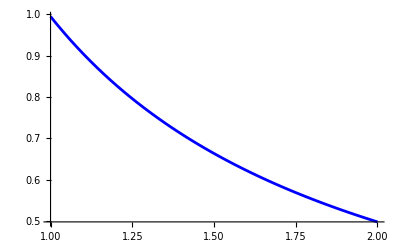

```mathematica
plotvexact=Plot[v[r]/.repv/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

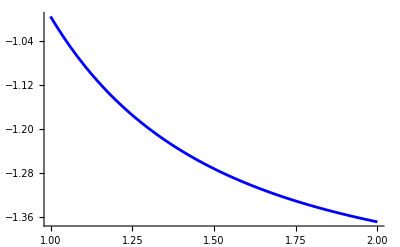

```mathematica
plotσexact=Plot[Evaluate[σ[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

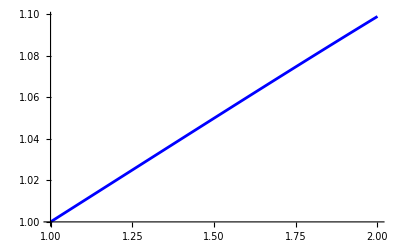

```mathematica
plotzexact=Plot[Evaluate[z[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

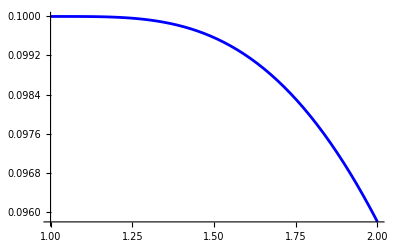

```mathematica
plotωexact=Plot[z'[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

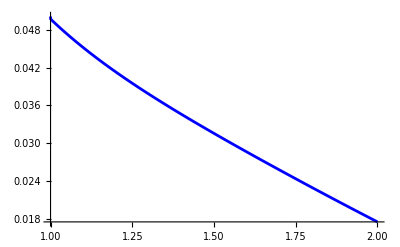

```mathematica
plotμexact=Plot[H[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

```mathematica
(*Compare with the solution from FE*)
```

```mathematica
(*check of v*)
```

```mathematica
tabv=Import["~/Documents/finite_elements/steady-state-flow/solution/v.csv"];
tabv=Table[{Norm[{tabv[[i,4]],tabv[[i,5]]}],Norm[{tabv[[i,1]],tabv[[i,2]]}]},{i,2,Length[tabv]}]
```

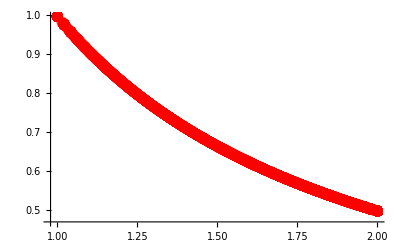

```mathematica
plotvfe=ListPlot[tabv,PlotRange->Full,PlotStyle->{PointSize->.02,Red,Opacity[0.1]}]
```

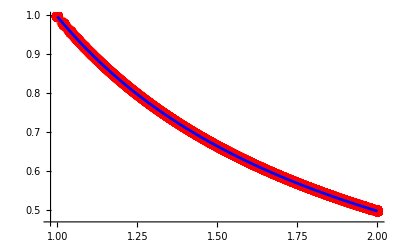

```mathematica
Show[plotvfe,plotvexact]
```

```mathematica
(*check of sigma*)
```

```mathematica
tabσ=Import["~/Documents/finite_elements/steady-state-flow/solution/sigma.csv"];
tabσ=Table[{Norm[{tabσ[[i,2]],tabσ[[i,3]]}],tabσ[[i,1]]},{i,2,Length[tabσ]}]
```

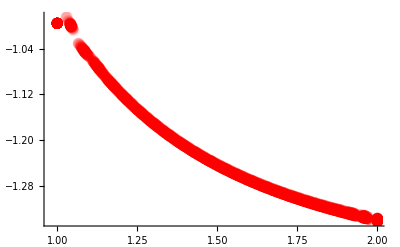

```mathematica
plotσfe=ListPlot[tabσ,PlotRange->Full,PlotStyle->{PointSize->.02,Red,Opacity[0.1]}]
```

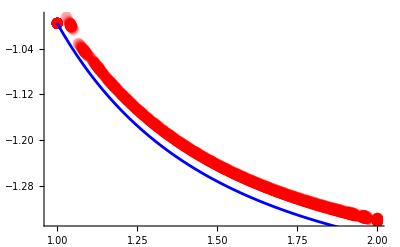

```mathematica
Show[plotσfe,plotσexact]
```

```mathematica
(*check of z*)
```

```mathematica
tabz=Import["~/Documents/finite_elements/steady-state-flow/solution/z.csv"];
tabz=Table[{Norm[{tabz[[i,2]],tabz[[i,3]]}],tabz[[i,1]]},{i,2,Length[tabz]}]
```

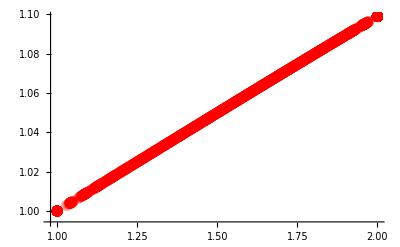

```mathematica
plotzfe=ListPlot[tabz,PlotRange->Full,PlotStyle->{PointSize->.02,Red,Opacity[0.1]}]
```

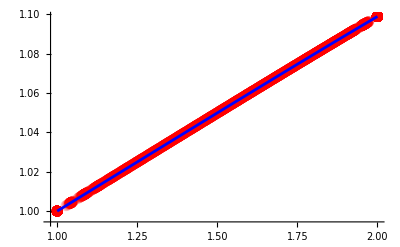

```mathematica
Show[plotzfe,plotzexact]
```

```mathematica
(*check of ω*)
```

```mathematica
tabω=Import["~/Documents/finite_elements/steady-state-flow/solution/omega.csv"];
tabω=Table[{Norm[{tabω[[i,4]],tabω[[i,5]]}],({tabω[[i,4]],tabω[[i,5]]}/Norm[{tabω[[i,4]],tabω[[i,5]]}]).{tabω[[i,1]],tabω[[i,2]]}},{i,2,Length[tabω]}]
```

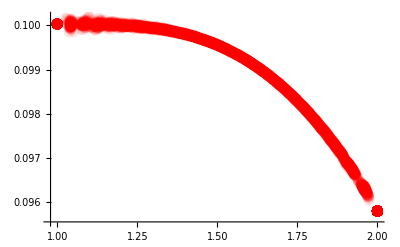

```mathematica
plotωfe=ListPlot[tabω,PlotRange->Full,PlotStyle->{PointSize->.02,Red,Opacity[0.1]}]
```

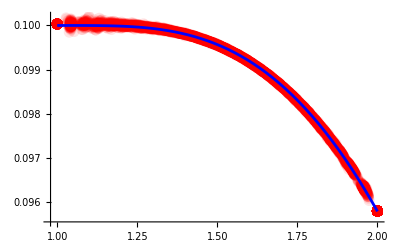

```mathematica
Show[plotωfe,plotωexact]
```

```mathematica
(*check of μ*)
```

```mathematica
tabμ=Import["~/Documents/finite_elements/steady-state-flow/solution/mu.csv"];
tabμ=Table[{Norm[{tabμ[[i,2]],tabμ[[i,3]]}],tabμ[[i,1]]},{i,2,Length[tabμ]}]
```

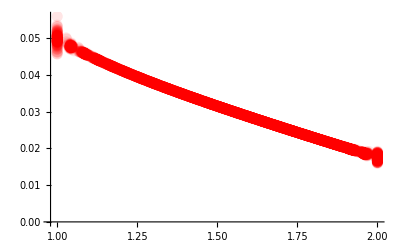

```mathematica
plotμfe=ListPlot[tabμ,PlotRange->Full,PlotStyle->{PointSize->.02,Red,Opacity[0.1]}]
```

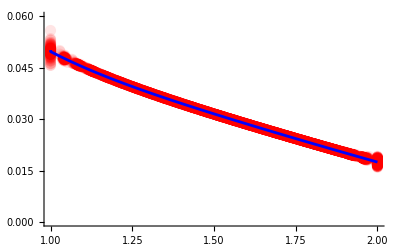

```mathematica
Show[plotμfe,plotμexact,PlotRange->{0,0.06}]
```

```mathematica
(*sign*)
```

```mathematica
(*check sigma*)
```

```mathematica
tabσ=Import["~/Documents/finite_elements/solution-flow-ring/resolution_0.3/sigma.csv"]
tabσ=Table[{Norm[{tabσ[[i,2]],tabσ[[i,3]]}],tabσ[[i,1]]},{i,2,Length[tabσ]}]
```

```mathematica
tabσresolution002 =;
```

```mathematica
tabσresolution005=;
```

```mathematica
tabσresolution01=;
```

```mathematica
tabσresolution03=;
```

```mathematica
plotσfe=Show[ListPlot[tabσresolution03,PlotStyle->{PointSize->.02,Red,Opacity[0.1]}]]
```

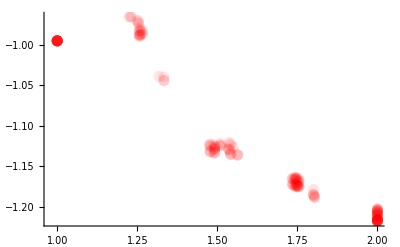

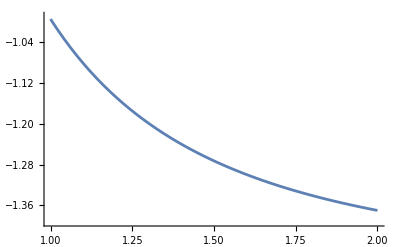

```mathematica
Show[plotσexact,ListPlot[tabσresolution002,PlotStyle->{PointSize->.02,Red,Opacity[0.001]}]]
```

```mathematica
deg=4;
```

```mathematica
f[r_]:=Sum[A[i]r^i,{i,0,deg}]
```

```mathematica
fitr03=FindFit[Select[tabσresolution03,#[[1]]>1.1&],f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→16.1196,A[1]→-38.7811,A[2]→32.8254,A[3]→-12.3765,A[4]→1.74633}

```mathematica
fitr01=FindFit[Select[tabσresolution01,#[[1]]>1.1&],f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→1.71319,A[1]→-5.44928,A[2]→3.95233,A[3]→-1.35265,A[4]→0.179874}

```mathematica
fitr005=FindFit[Select[tabσresolution005,#[[1]]>1.1&],f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→1.96899,A[1]→-6.1112,A[2]→4.52858,A[3]→-1.57389,A[4]→0.211487}

```mathematica
fitr002=FindFit[Select[tabσresolution002,#[[1]]>1.1&],f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→1.90116,A[1]→-5.97606,A[2]→4.40168,A[3]→-1.52143,A[4]→0.203422}

```mathematica
(*sigma extrapolated to resolution -> 0*)
```

```mathematica
Clear[ϵ]
```

```mathematica
finf[rs_]:=α/.FindFit[{{0.3,f[rs]/.fitr03},{0.1,f[rs]/.fitr01},{0.05,f[rs]/.fitr005},{0.02,f[rs]/.fitr002}},α+β x+γ x^2+ϵ x^3,{α,β,γ,ϵ},x]
```

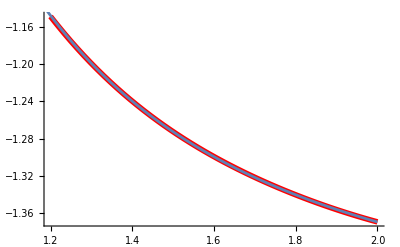

```mathematica
Show[Plot[finf[rs],{rs,1.2,Rmax},PlotStyle->{Red,Thickness->0.01}],plotσexact]
```

```mathematica
(*r=0.3*)
```

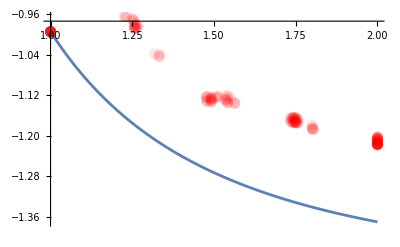

```mathematica
(*r=0.1*)
```

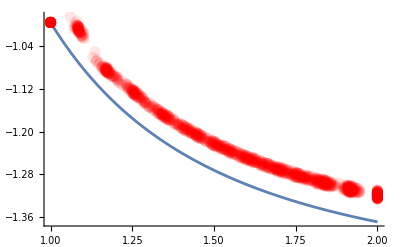

```mathematica
(*r=0.05*)
```

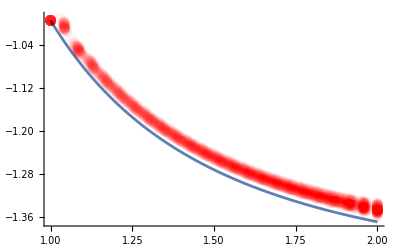

```mathematica
(*r=0.025*)
```